```mathematica
ClearAll[Nk];
Nk=Range[0,3,0.2];
fNR[ϵ_]:=2/Sqrt[Pi+Nk*ϵ^1.5]*Exp[-(ϵ+0.8*Nk*ϵ^2.5+(8/25)*Nk^2*ϵ^4)/(1+0.8*Nk*ϵ^1.5)];
NkList=NIntegrate[fNR[x],{x,0,Infinity}]
```

{1.12838,1.02276,0.940466,0.879808,0.832332,0.793586,0.761015,0.733028,0.708572,0.686914,0.667523,0.650005,0.634057,0.619444,0.605977,0.593506}

```mathematica
data={};
For[i=0,i<Length[NkList],i++;data=Append[data,{Nk[[i]],NkList[[i]]}]]
```

```mathematica
data
```

{{0.,1.12838},{0.2,1.02276},{0.4,0.940466},{0.6,0.879808},{0.8,0.832332},{1.,0.793586},{1.2,0.761015},{1.4,0.733028},{1.6,0.708572},{1.8,0.686914},{2.,0.667523},{2.2,0.650005},{2.4,0.634057},{2.6,0.619444},{2.8,0.605977},{3.,0.593506}}

```mathematica
model=a0*x^4+a1*x^3+a2*x^2+a3*x+a4;
fit=FindFit[data,model,{a0,a1,a2,a3,a4},x]
```

{a0→0.0123783,a1→-0.10184,a2→0.325538,a3→-0.571237,a4→1.1263}

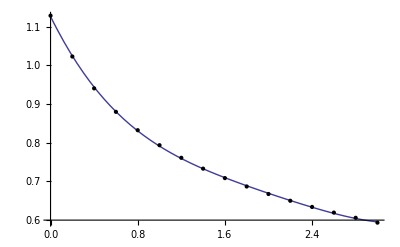

```mathematica
Plot[model/.fit,{x,0,3},Epilog->{Point[data]}]
```